```mathematica
f[_z]:=z^-1
```

```mathematica
p1[s_] := ParametricPlot[ReIm[t+0.5 I],{t,-s,s}, AxesOrigin -> {0,0},PlotRange ->{{-5,5},{0,1}} ]
```

```mathematica
q1[s_] := ParametricPlot[ReIm[1/(t+0.5 I)],{t,-s,s}, AxesOrigin -> {0,0},PlotRange ->{{-2,2},{-2.5,.5}} ]
```

```mathematica
Manipulate[{p1[s],q1[s]}, {s, 0.1, 5}]
```

```mathematica
Manipulate[{p1[s],q1[s]},{s,0.1,4}]
```

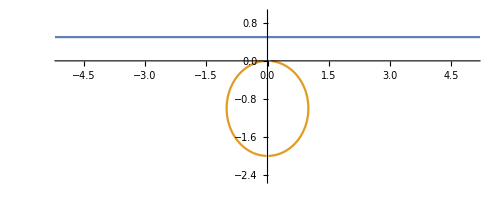

```mathematica
ParametricPlot[{ReIm[t+0.5 I],ReIm[1/(t+0.5 I)]},{t,-10,10}, AxesOrigin->{0,0},PlotRange->{{-5,5},{-2.5,1}}]
```

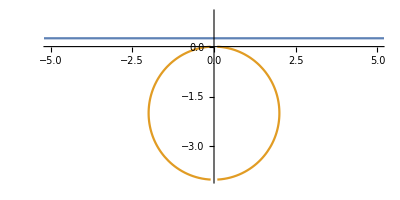

```mathematica
ParametricPlot[{ReIm[t+0.25I],ReIm[1/(t+0.25 I)]},{t,-10,10}, AxesOrigin->{0,0},PlotRange->{{-5,5},{-4,1}}]
```

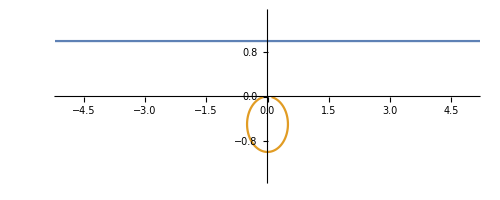

```mathematica
ParametricPlot[{ReIm[t+0+I],ReIm[1/(t+ I)]},{t,-10,10}, AxesOrigin->{0,0},PlotRange->{{-5,5},{-1.5,1.5}}]
```

```mathematica
Graphics[HalfPlane[{{0,0.5},{2,0.5}},{0,1}],Frame->True]
```

-Graphics-

```mathematica
ParametricPlot[ReIm[1/(x+I y)], {x,y}∈HalfPlane[{{0,0.5},{50,0.5}},{0,1}]]
```

-Graphics-

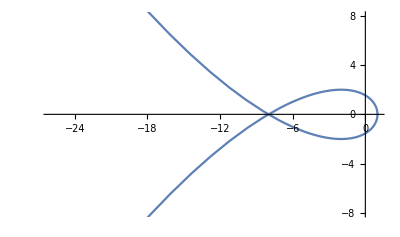

```mathematica
ParametricPlot[ReIm[(1+I t)^3], {t, -3,3}]
```